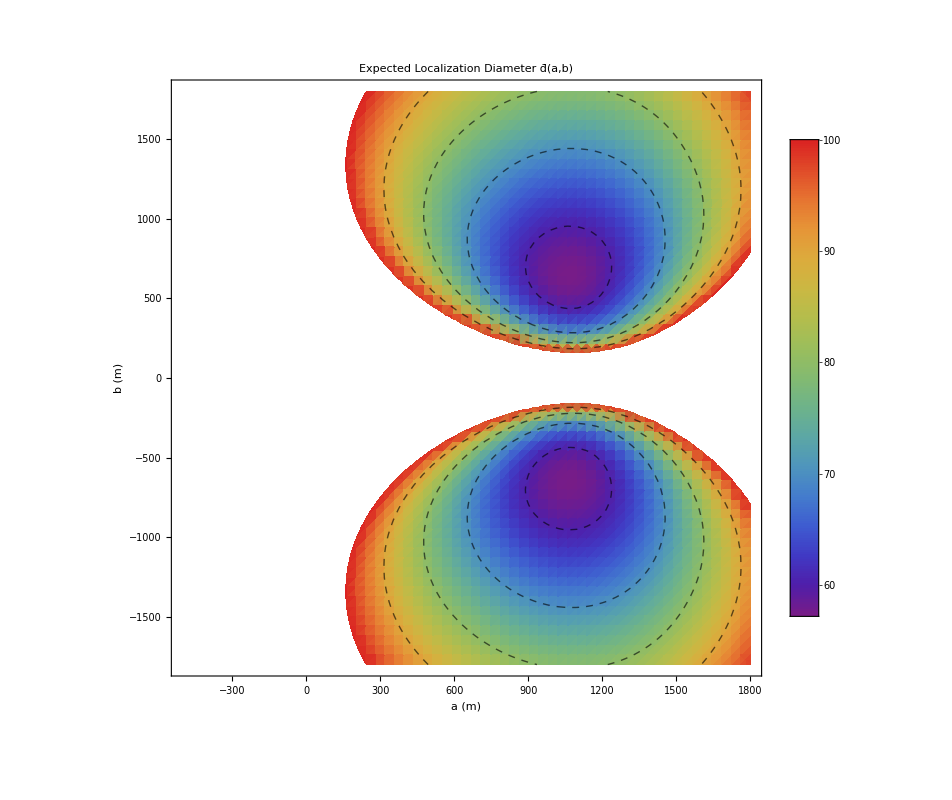

```mathematica
(* ============================================================*)(*Q2:期望定位区域直径 dbar(a,b) 的二维热力图*)(*带坐标轴、带图例，叠加等高线，导出为图片*)(* ============================================================*)(*----参数（与你原代码一致）----*)h=1500.;
alpha=1. Degree;

(*----两直线交点----*)
intersect2Lines[P1_,th1_,P2_,th2_]:=Module[{u1,u2,diff,denom,t1},u1={Cos[th1],Sin[th1]};
u2={Cos[th2],Sin[th2]};
diff=P2-P1;
denom=u1[[1]] u2[[2]]-u1[[2]] u2[[1]];
If[Abs[denom]<10^-8,Return[None]];
t1=(diff[[1]] u2[[2]]-diff[[2]] u2[[1]])/denom;
P1+t1 u1];

(*----交会四边形顶点----*)
quadVertices[x0_,a_,b_]:=Module[{P1={0.,0.},P2={a,b},dir,th2,thP,thM,v},dir={x0-a,-b};
If[Norm[dir]<10^-6,Return[None]];
th2=ArcTan[dir[[1]],dir[[2]]];
thP=th2+alpha;
thM=th2-alpha;
v={intersect2Lines[P1,alpha,P2,thP],intersect2Lines[P1,alpha,P2,thM],intersect2Lines[P1,-alpha,P2,thM],intersect2Lines[P1,-alpha,P2,thP]};
If[MemberQ[v,None],Return[None]];
v];

(*----四边形直径----*)
quadDiameter[verts_]:=Module[{n=Length[verts],mx=0.},Do[Do[mx=Max[mx,Norm[verts[[i]]-verts[[j]]]],{j,i+1,n}],{i,1,n}];
mx];

(*----期望直径----*)
expectedD[a_?NumericQ,b_?NumericQ,n_Integer:50]:=Module[{xs,fs,vals,total,totalW},xs=Table[h (k+0.5)/n,{k,0,n-1}];
fs=2. xs/h^2;
vals=Table[Module[{vs=quadVertices[xs[[k]],a,b]},If[vs===None,Indeterminate,quadDiameter[vs]]],{k,1,n}];
If[MemberQ[vals,Indeterminate],Return[Indeterminate]];
total=Total[fs vals];
totalW=Total[fs];
total/totalW];

(* ============================================================*)
(*绘图：带坐标轴、带图例、叠加等高线*)
(* ============================================================*)

plot2D=Show[(*底层：热力图*)DensityPlot[expectedD[a,b,50],{a,-500,1800},{b,-1800,1800},PlotRange->{0,100},PlotPoints->60,MaxRecursion->1,ColorFunction->"Rainbow",ColorFunctionScaling->True,Frame->True,FrameLabel->{Style["a (m)",16,Bold,Black],Style["b (m)",16,Bold,Black]},FrameStyle->Directive[Black,12],FrameTicksStyle->Directive[Black,12],PlotLabel->Style["Expected Localization Diameter \!\(\*OverscriptBox[\(d\), \(_\)]\)(a,b)",18,Bold,Black],PlotLegends->Automatic,Mesh->None,BoundaryStyle->None],(*上层：等高线*)ContourPlot[expectedD[a,b,50],{a,-500,1800},{b,-1800,1800},PlotRange->{0,100},PlotPoints->60,MaxRecursion->1,Contours->{10,20,30,40,50,60,70,80,90},ContourShading->None,ContourStyle->Directive[Black,Opacity[0.6],Dashed]],ImageSize->800,Frame->True,FrameLabel->{Style["a (m)",16,Bold,Black],Style["b (m)",16,Bold,Black]}];

(*----显示----*)
plot2D

(* ============================================================*)
(*导出为图片*)
(* ============================================================*)

Export["Q2_expected_diameter_heatmap.png",plot2D,ImageResolution->300];

(*如需同时导出 PDF 矢量图，取消下面注释即可*)
Export["Q2_expected_diameter_heatmap.pdf",plot2D];
```

```mathematica
Directory[]                          (*查看当前工作目录*)
AbsoluteFileName["Q2_expected_diameter_heatmap.png"]  (*查看该文件的绝对路径*)
```

C:\Users\lenovo

C:\Users\lenovo\Q2_expected_diameter_heatmap.png